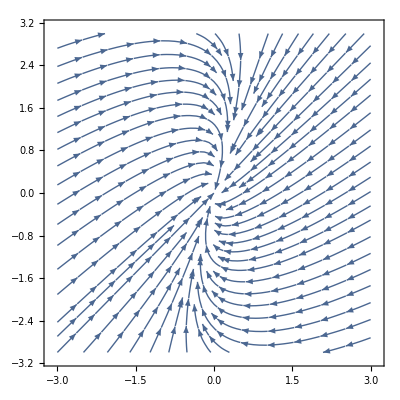

```mathematica
(* Here we classify equilibrium points for constant coefficient homogeneous two-dimensional systems (autonomous) *)

(* This is an example of a sink *)

a1=StreamPlot[{-5x+y,-3x-y},{x,-3,3},{y,-3,3},Axes -> True]
```

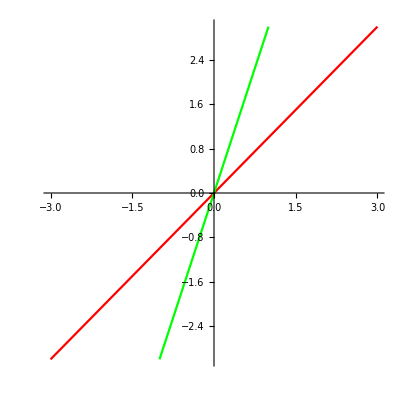

```mathematica
(* The eigenvectors are (1,1) and (1,3) which we plot here *)
b1=ParametricPlot[{{3t,3t},{t,3t}},{t,-1,1},PlotStyle->{Red, Green}]
```

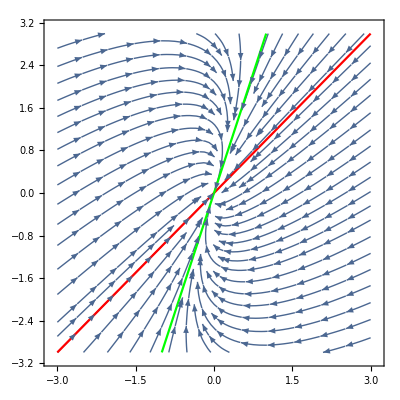

```mathematica
(* We now plot the eigenvectors with the streamplot *)
Show[a1,b1]
```

```mathematica
(* If we reverse the sign of A, we end up with a source *)
```

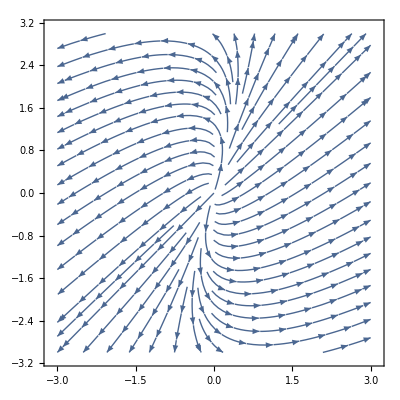

```mathematica
StreamPlot[{5x-y,3x+y},{x,-3,3},{y,-3,3},Axes -> True]
```

```mathematica
(* If our eigenvalues are real but have different signs, then we have a saddle point *)
```

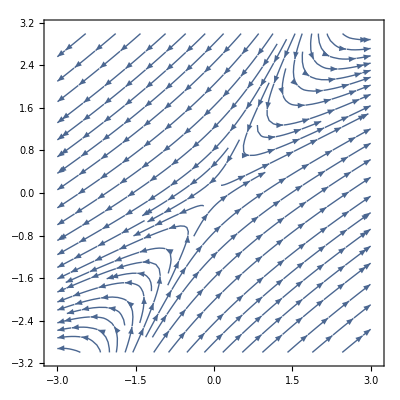

```mathematica
a2=StreamPlot[{3x-2y,2x-2y},{x,-3,3},{y,-3,3},Axes -> True]
```

```mathematica
(* The eigenvectors are (2,1) and (1,2) *)
```

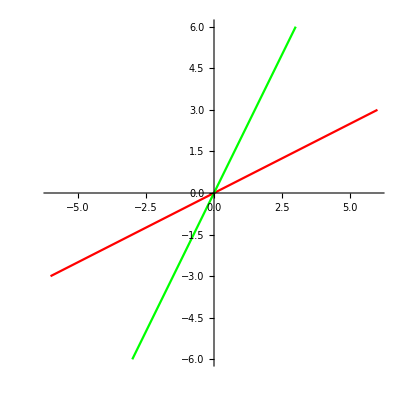

```mathematica
b2=ParametricPlot[{{6t,3t},{3t,6t}},{t,-1,1},PlotStyle->{Red, Green}]
```

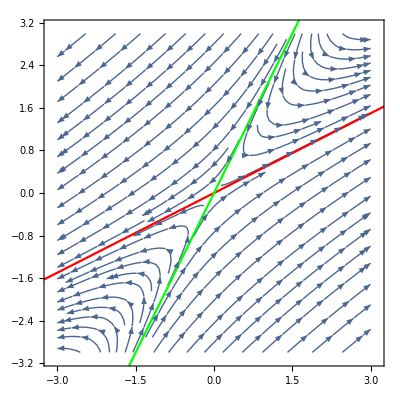

```mathematica
Show[a2,b2]
```

```mathematica
(* If the eigenvalues are purely imaginary, then we have a center *)
```

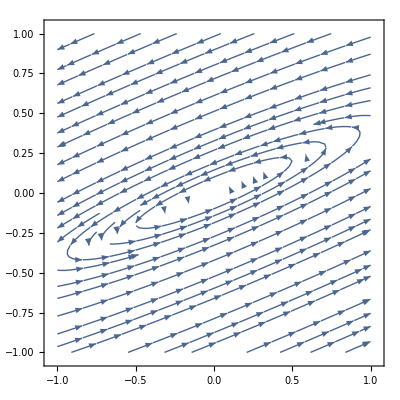

```mathematica
StreamPlot[{2x-5y,x-2y},{x,-1,1},{y,-1,1},Axes -> True]
```

```mathematica
(* If the eigenvalues are comples a+bi and a-bi with a<0, we have a spiral sink *)
```

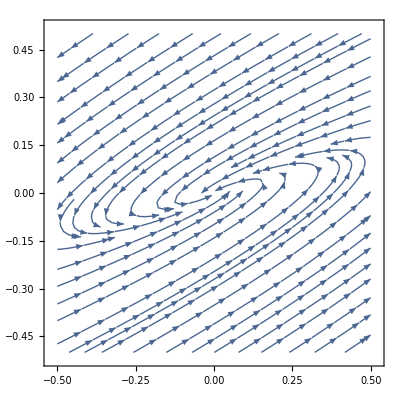

```mathematica
StreamPlot[{x-5y,x-3y},{x,-.5,.5},{y,-.5,.5},Axes -> True]
```

```mathematica
(* If the eigenvalues are comples a+bi and a-bi with a>0, we have a spiral source *)
```

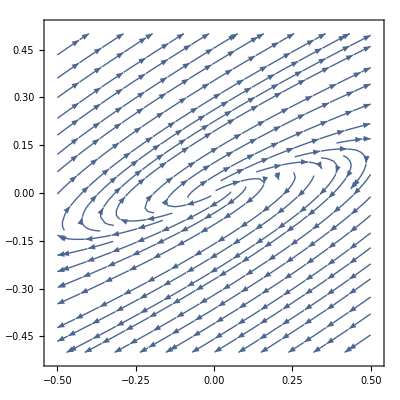

```mathematica
StreamPlot[{-x+5y,-x+3y},{x,-.5,.5},{y,-.5,.5},Axes -> True]
```

```mathematica
(* If we have only one eigenvalue (nonzero) and two eigenvectors, then we get a star point. Note that any vector is an eigenvector *)
```

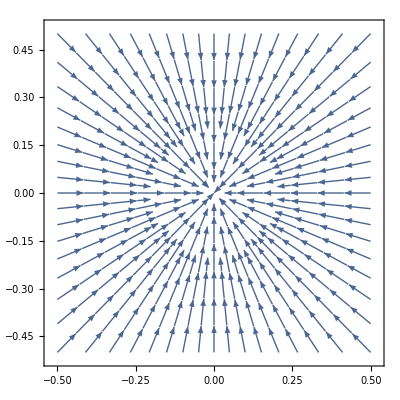

```mathematica
StreamPlot[{-2x,-2y},{x,-.5,.5},{y,-.5,.5},Axes -> True]
```

```mathematica
(* If we have only one eigenvalue (nonzero) and one eigenvector, then we get an improper node.  *)
```

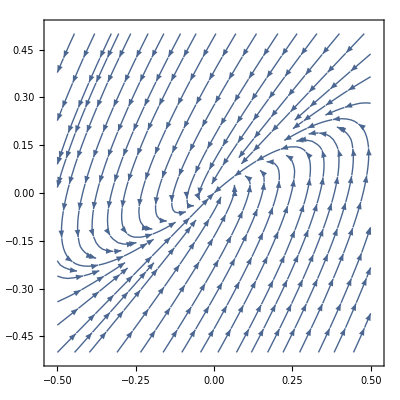

```mathematica
a3=StreamPlot[{x-4y,4x-7y},{x,-.5,.5},{y,-.5,.5},Axes -> True]
```

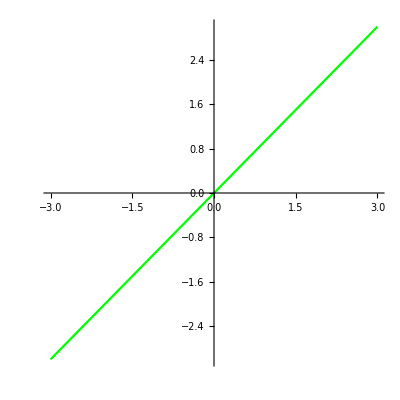

```mathematica
(*The eigenvector is (1,1) and the generalized eigenvector is (1/4,0). As t -> infinity or - infinity only the eigenvector (1,1) will dominate *)
b3=ParametricPlot[{3t,3t},{t,-1,1},PlotStyle->{Red, Green}]
```

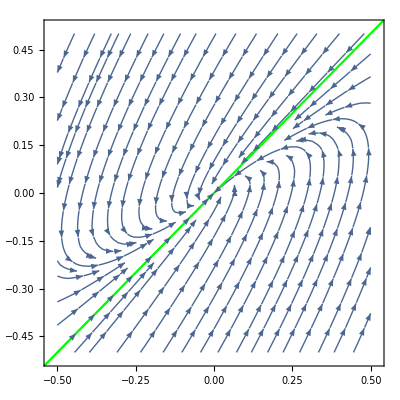

```mathematica
Show[a3,b3]
```